# Two-level system.

# Tilted Liouvillian generator

```mathematica
(* Hamiltonian *)
H0[Ω_]:=  Ω {{1,0},{0,0}};

(* Observable *)
oX[θ_]:=  Cos[θ]*PauliMatrix[1] + Sin[θ]*PauliMatrix[3];

(* Parametrization density matrix *)
rho={{Subscript[r, ee],ru-I rv},{ru+I rv,1-Subscript[r, ee]}};

(*** Jump operator clock subspace***)
Lw = {{0,0},{1,0}}; 
Lwd = {{0,1},{0,0}};

(* Vectorization of the tilted Liouvillian generator *)
ldss[Ω_,γm_,γw_,θ_,s_] := Module[{},
                       -ⅈ (KroneckerProduct[H0[Ω],IdentityMatrix[2]]- 
                           KroneckerProduct[IdentityMatrix[2],Transpose[H0[Ω]]])
                       -γm (KroneckerProduct[oX[θ].oX[θ],IdentityMatrix[2]]
                            - 2 KroneckerProduct[oX[θ],Transpose[oX[θ]]]
                            + KroneckerProduct[IdentityMatrix[2],Transpose[oX[θ].oX[θ]]])
                       +γw (Exp[-s] KroneckerProduct[Lw,Transpose[Lwd]] 
                             - 1/2( KroneckerProduct[Lwd.Lw, IdentityMatrix[2]] 
                             + KroneckerProduct[IdentityMatrix[2],Transpose[Lwd.Lw]] ))                      
                       ]
```

# Solution steady state (s=0)

```mathematica
Ω=.;γm=.;γw=.; θ=.;

FullSimplify[Solve[-ⅈ(H0[Ω].rho-rho.H0[Ω])-γm (oX[θ].(oX[θ].rho-rho.oX[θ])-(oX[θ].rho-rho.oX[θ]).oX[θ])
+γw(Lw.rho.Lwd-1/2(rho.Lwd.Lw+Lwd.Lw.rho))
=={{0,0},{0,0}},{Subscript[r, ee],ru,rv}],Assumptions -> {Ω ∈ Reals, γm > 0, γw > 0, θ ∈ Reals}]
```

{{r_ee→-(2 γm (8 γm γw+γw^2+4 Ω^2) Cos[θ]^2)/(-γw (6 γm+γw) (8 γm+γw)-4 (2 γm+γw) Ω^2+2 γm (8 γm γw+γw^2-4 Ω^2) Cos[2 θ]),ru→(2 γm γw (8 γm+γw) Sin[2 θ])/(-γw (6 γm+γw) (8 γm+γw)-4 (2 γm+γw) Ω^2+2 γm (8 γm γw+γw^2-4 Ω^2) Cos[2 θ]),rv→(8 γm γw Ω Cos[θ] Sin[θ])/(-γw (6 γm+γw) (8 γm+γw)-4 (2 γm+γw) Ω^2+2 γm (8 γm γw+γw^2-4 Ω^2) Cos[2 θ])}}

# Large Deviation Theory: mean and variance of clock ticks

### Mean Rate + Transient Contributions

```mathematica
idVec =  {1,0,0,1};                                               (* Vectorized Identity *)
L0[Ω_, γm_, γw_, θ_] := ldss[Ω, γm, γw, θ, 0];                  (* Liouvillian for s=0 *)
L1[Ω_, γm_, γw_, θ_] := D[ldss[Ω, γm, γw, θ, s], s] /. s -> 0;   (* For this model: L1 = -γw KroneckerProduct[Lw, Transpose[Lwd]] *)

(* General qubit initial state rho0 *)
rho0 [p_,q_]   := {{p, q}, {Conjugate[q], 1 - p}};
rho0vec[p_,q_] := Flatten[rho0[p,q]];
```

```mathematica
(* Steady state: nullspace of L0, normalized to unit trace. *)
rhoSSvecRaw[Ω_, γm_, γw_, θ_]:= First[NullSpace[L0[Ω, γm, γw, θ]]]                          

rhoSSvec[Ω_, γm_, γw_, θ_]   := rhoSSvecRaw[Ω, γm, γw, θ]/(idVec.rhoSSvecRaw[Ω, γm, γw, θ]); 

(* Dominant eigenvalue slope/ mean rate *)
lam1[Ω_, γm_, γw_, θ_]     := idVec.L1[Ω, γm, γw, θ].rhoSSvec[Ω, γm, γw, θ];     (* lam'_dom(0) *)
meanRate[Ω_, γm_, γw_, θ_] :=  -lam1[Ω, γm, γw, θ];                               (* k_ss = γw Tr[Lwd.Lw.rho_ss] *) 
 

(* ---------- Initial-state transient constant ---------- *)

(* Drazin inverse: LD = Inverse[L0 + P] - P, P = |rho_ss>><<1| *)
P[Ω_, γm_, γw_, θ_]   := KroneckerProduct[rhoSSvec[Ω, γm, γw, θ], idVec];
LD [Ω_, γm_, γw_, θ_] := Inverse[L0 [Ω, γm, γw, θ]+ P[Ω, γm, γw, θ]] - P[Ω, γm, γw, θ];

(* Initial State Correction for the Mean: -c'_dom(0)/c_dom(0) *)
meanRateCorr [Ω_, γm_, γw_, θ_,p_,q_] := idVec.L1[Ω, γm, γw, θ].LD[Ω, γm, γw, θ].rho0vec[p,q];
```

```mathematica
Ω =.; γw=.;γm=.;θ=.;

(* Dominant eigenvalue/ mean rate *)
FullSimplify[meanRate[Ω, γm, γw, θ], Assumptions -> {Ω ∈ Reals, γm > 0, γw > 0}]

(* ---------- Initial-state transient constant ---------- *)
FullSimplify[meanRateCorr [Ω, γm, γw, θ,0,0], Assumptions -> {Ω ∈ Reals, γm > 0, γw > 0}]

(* Optional consistency checks (should all give zero):*)
 Simplify[L0 [Ω, γm, γw, θ]. LD [Ω, γm, γw, θ]. L0 [Ω, γm, γw, θ]- L0[Ω, γm, γw, θ]];
 Simplify[LD [Ω, γm, γw, θ]. L0 [Ω, γm, γw, θ]. LD [Ω, γm, γw, θ]- LD[Ω, γm, γw, θ]];
 Simplify[idVec . LD[Ω, γm, γw, θ]];
Simplify[LD [Ω, γm, γw, θ]. rhoSSvec[Ω, γm, γw, θ]];
```

-(2 γm γw (8 γm γw+γw^2+4 Ω^2) Cos[θ]^2)/(-γw (6 γm+γw) (8 γm+γw)-4 (2 γm+γw) Ω^2+2 γm (8 γm γw+γw^2-4 Ω^2) Cos[2 θ])

(2 γm γw Cos[θ]^2 ((4 γm-γw) γw (8 γm+γw)^2-8 (16 γm^2+14 γm γw+γw^2) Ω^2-16 Ω^4-4 γm (γw (8 γm+γw)^2-4 (8 γm+3 γw) Ω^2) Cos[2 θ]))/((γw (6 γm+γw) (8 γm+γw)+4 (2 γm+γw) Ω^2-2 γm (8 γm γw+γw^2-4 Ω^2) Cos[2 θ])^2)

Zero Stationary Boundary Term (offset at the steady state)

```mathematica
Simplify[idVec . L1[Ω, γm, γw, θ] . LD [Ω, γm, γw, θ]. rhoSSvec[Ω, γm, γw, θ], Assumptions ->  {Ω ∈ Reals, γm > 0, γw > 0}]
```

0

Plots

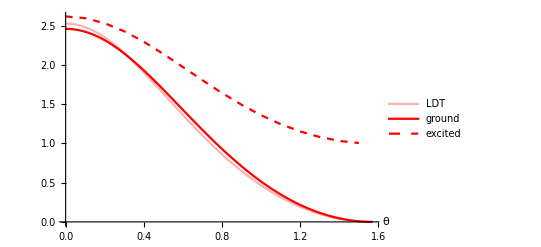

```mathematica
Ω=1;γw=6;γm=8; 
meanAna= ListPlot[Table[{θ,meanRate [Ω, γm, γw, θ]},{θ,0,π/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Directive[Solid,Red,Opacity[0.3]],AxesLabel->{Style["θ",20,Black]}];
meanAnaCorrGround= ListPlot[Table[{θ,meanRate [Ω, γm, γw, θ]+meanRateCorr [Ω, γm, γw, θ,0,0]},{θ,0,π/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Directive[Solid,Red,Opacity[1]],AxesLabel->{Style["γ_m",20,Black]}];
meanAnaCorrExcited= ListPlot[Table[{θ,meanRate [Ω, γm, γw, θ]+meanRateCorr [Ω, γm, γw, θ,1,0]},{θ,0,π/2,0.10}],Joined->True,PlotRange->All,PlotStyle->Directive[Dashed,Red,Opacity[1]],AxesLabel->{Style["γ_m",20,Black]}];
Legended[Show[meanAna,meanAnaCorrGround,meanAnaCorrExcited,PlotRange->All],LineLegend[{Directive[Red,Opacity[0.3],Solid],Directive[Red,Opacity[1],Solid],Directive[Red,Opacity[1],Dashed]},{"LDT","ground","excited"}]]
```

### Variance rate + Transient Contributions

```mathematica
(* Second-order piece of the tilted generator: L2 = (1/2) d^2/ds^2 L_s |_0 *)
(* For this model: L2mat = -(1/2) L1 = (γw/2) KroneckerProduct[Lw, Transpose[Lwd]] *)
L2 [Ω_, γm_, γw_, θ_] := Simplify[(1/2) (D[ldss[Ω, γm, γw, θ, s], {s, 2}] /. s -> 0)];
LD2[Ω_, γm_, γw_, θ_] := LD[Ω, γm, γw, θ].LD[Ω, γm, γw, θ];   

(* ---------- Variance rate ---------- *)
lam2[Ω_, γm_, γw_, θ_]    := Simplify[ idVec.L2[Ω, γm, γw, θ].rhoSSvec[Ω, γm, γw, θ] - idVec.L1[Ω, γm, γw, θ].LD[Ω, γm, γw, θ].L1[Ω, γm, γw, θ].rhoSSvec[Ω, γm, γw, θ], Assumptions -> $assume];
varRate[Ω_, γm_, γw_, θ_] := 2 lam2[Ω, γm, γw, θ];

(* ---------- Initial-state transient constant ---------- *)
(* Gauge: <<1|r(s)>> = 1 to all orders, so everything sits in the left vector.  *)

(* row vector <<l1| *)
l1vec[Ω_, γm_, γw_, θ_] := -idVec.L1[Ω, γm, γw, θ].LD[Ω, γm, γw, θ];             
          
(* row vector <<l2| *)
l2vec[Ω_, γm_, γw_, θ_] := (-(idVec.L1 [Ω, γm, γw, θ].LD2[Ω, γm, γw, θ].L1[Ω, γm, γw, θ].rhoSSvec[Ω, γm, γw, θ]) idVec 
                            - lam1[Ω, γm, γw, θ] (idVec.L1[Ω, γm, γw, θ].LD2[Ω, γm, γw, θ])  
                            + idVec.L1 [Ω, γm, γw, θ].LD[Ω, γm, γw, θ].L1[Ω, γm, γw, θ].LD[Ω, γm, γw, θ] 
                            - idVec.L2[Ω, γm, γw, θ].LD[Ω, γm, γw, θ]);  
                                                 
(* Initial State Correction for the Variance *)
varRateCorr[Ω_, γm_, γw_, θ_,p_,q_] := 2 (l2vec[Ω, γm, γw, θ].rho0vec[p,q]) - (l1vec[Ω, γm, γw, θ].rho0vec[p,q])^2;
```

```mathematica
Ω=.;γw=.;γm=.;θ =.;

(* ---------- Variance rate ---------- *)
FullSimplify[varRate[Ω, γm, γw, θ], Assumptions -> {Ω ∈ Reals, γm > 0, γw > 0, θ ∈ Reals}]

(* ---------- Initial-state transient constant ---------- *)
FullSimplify[varRateCorr[Ω, γm, γw, θ,1,0], Assumptions ->{Ω ∈ Reals, γm > 0, γw > 0, θ ∈ Reals}]
```

(2 γm γw (8 γm γw+γw^2+4 Ω^2) Cos[θ]^2 (-γw^2 (8 γm+γw)^2 (42 γm^2+10 γm γw+γw^2)-8 γw (64 γm^3+52 γm^2 γw+14 γm γw^2+γw^3) Ω^2-16 (6 γm^2+2 γm γw+γw^2) Ω^4+2 γm ((3 γw^2 (4 γm+γw) (8 γm+γw)^2+8 γw (-4 γm+γw) (8 γm+γw) Ω^2-16 (4 γm+γw) Ω^4) Cos[2 θ]+γm (γw^2 (8 γm+γw)^2-16 γw^2 Ω^2-16 Ω^4) Cos[4 θ])))/(-γw (6 γm+γw) (8 γm+γw)-4 (2 γm+γw) Ω^2+2 γm (8 γm γw+γw^2-4 Ω^2) Cos[2 θ])^3

-((2 γm γw Cos[θ]^2 (γw^3 (8 γm+γw)^4 (-96 γm^3+6 γm^2 γw-γm γw^2+γw^3)+16 γw^2 (8 γm+γw) (2944 γm^5+1792 γm^4 γw+234 γm^3 γw^2+85 γm^2 γw^3+18 γm γw^4+γw^5) Ω^2+32 γw (-2560 γm^5-1408 γm^4 γw-376 γm^3 γw^2+216 γm^2 γw^3+55 γm γw^4+3 γw^5) Ω^4+256 (-16 γm^4-86 γm^3 γw-33 γm^2 γw^2+8 γm γw^3+γw^4) Ω^6+256 (-6 γm+γw) (γm+γw) Ω^8+γm (γw^3 (8 γm+γw)^4 (248 γm^2+24 γm γw-9 γw^2)-16 γw^2 (8 γm+γw) (3904 γm^4+3552 γm^3 γw+1463 γm^2 γw^2+232 γm γw^3+12 γw^4) Ω^2-32 γw^2 (4608 γm^3+3496 γm^2 γw+664 γm γw^2+37 γw^3) Ω^4-256 (8 γm^3+63 γm^2 γw+72 γm γw^2+10 γw^3) Ω^6-256 (8 γm+5 γw) Ω^8) Cos[2 θ]+2 γm^2 (-γw^3 (8 γm+γw)^4 (80 γm+23 γw)+8 γw^2 (8 γm+γw) (1152 γm^3+768 γm^2 γw+342 γm γw^2+35 γw^3) Ω^2+128 γw (320 γm^3+368 γm^2 γw+151 γm γw^2+14 γw^3) Ω^4+128 (16 γm^2+22 γm γw+9 γw^2) Ω^6-256 Ω^8) Cos[4 θ]+8 γm^3 (γw^3 (8 γm+γw)^4-2 γw^2 (8 γm+γw) (192 γm^2+32 γm γw+9 γw^2) Ω^2-96 γw^3 Ω^4-32 (-8 γm+γw) Ω^6) Cos[6 θ]))/(γw (6 γm+γw) (8 γm+γw)+4 (2 γm+γw) Ω^2-2 γm (8 γm γw+γw^2-4 Ω^2) Cos[2 θ])^4)

Stationary Boundary Term (offset at the steady state)

```mathematica
Ω=.;γw=.;γm=.; θ =0;
FullSimplify[-2 idVec . L1[Ω, γm, γw, θ] . LD2 [Ω, γm, γw, θ]. L1 [Ω, γm, γw, 0]. rhoSSvec[Ω, γm, γw, θ], Assumptions ->{Ω ∈ Reals, γm > 0, γw > 0}]
```

(8 γm^2 γw^2)/(4 γm+γw)^4

Plots

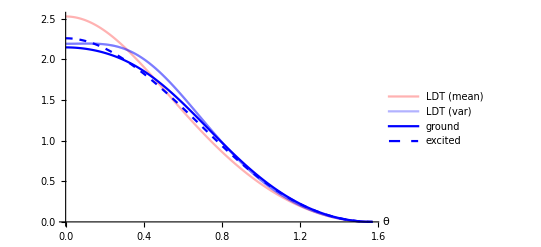

```mathematica
Ω=1;γw=6;γm=8; 
varAna = ListPlot[Table[{θ,varRate[Ω, γm, γw, θ]},{θ,0,π/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Directive[Solid,Blue,Opacity[0.3]],AxesLabel->{Style["θ",20,Black]}];
varAnaCorrGround = ListPlot[Table[{θ,varRate[Ω, γm, γw, θ]+varRateCorr[Ω, γm, γw, θ,0,0]},{θ,0,π/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Directive[Solid,Blue,Opacity[1]],AxesLabel->{Style["θ",20,Black]}];
varAnaCorrExcited= ListPlot[Table[{θ,varRate[Ω, γm, γw, θ]+varRateCorr [Ω, γm, γw, θ,1,0]},{θ,0,π/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Directive[Dashed,Blue,Opacity[1]],AxesLabel->{Style["θ",20,Black]}];
Legended[Show[meanAna, varAna ,varAna,varAnaCorrGround,varAnaCorrExcited,PlotRange->All],LineLegend[{Directive[Red,Opacity[0.3],Solid],Directive[Blue,Opacity[0.3],Solid],Directive[Blue,Opacity[1],Solid],Directive[Blue,Opacity[1],Dashed]},{"LDT (mean)","LDT (var)","ground","excited"}]]
```

### Time Evolution for X = σ_x to the Steady State (Mean and Variance)

#### Mean

```mathematica
meantime[Ω_, γm_, γw_,t_,p_,q_] := l1vec[Ω, γm, γw, 0].MatrixExp[t L0[Ω, γm, γw, 0]].rho0vec[p,q]-l1vec[Ω, γm, γw, 0].rho0vec [p,q]
```

```mathematica
Ω=.;γw=.;γm=.;

(* Initial state: Ground state *)
Collect[meantime[Ω, γm, γw,t,0,0]//FullSimplify,ⅇ^(-t (4 γm+γw)) ]

(* Initial state: Excited state *)
Collect[meantime[Ω, γm, γw,t,1,0]//FullSimplify,ⅇ^(-t (4 γm+γw)) ]
```

-(2 γm γw)/(4 γm+γw)^2+(2 ⅇ^(-t (4 γm+γw)) γm γw)/(4 γm+γw)^2

(γw (2 γm+γw))/(4 γm+γw)^2-(ⅇ^(-t (4 γm+γw)) γw (2 γm+γw))/(4 γm+γw)^2

Plots

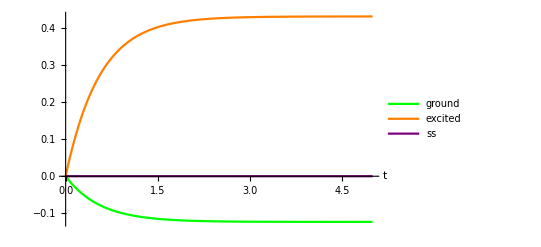

```mathematica
Ω=1;γw=1;γm=0.2; 
meanGroundEvol = ListPlot[Table[{t,-(2 γm γw)/(4 γm+γw)^2+(2 ⅇ^(-t (4 γm+γw)) γm γw)/(4 γm+γw)^2},{t,0,5,0.01}],Joined->True, PlotStyle->Directive[Solid,Green],AxesLabel->{Style["t",20,Black]}];

meanExcitedEvol = ListPlot[Table[{t,(γw (2 γm+γw))/(4 γm+γw)^2-(ⅇ^(-t (4 γm+γw)) γw (2 γm+γw))/(4 γm+γw)^2},{t,0,5,0.01}],Joined->True, PlotStyle->Directive[Solid,Orange],AxesLabel->{Style["t",20,Black]}];

meanSsEvol = ListPlot[Table[{t,0},{t,0,5,0.01}],Joined->True, PlotStyle->Directive[Solid,Purple],AxesLabel->{Style["t",20,Black]}];

Legended[Show[meanGroundEvol ,meanExcitedEvol,meanSsEvol  ,PlotRange->All],LineLegend[{Directive[Green,Solid],Directive[Orange,Solid],Directive[Solid,Purple]},{"ground","excited","ss"}]]
```

#### Variance

```mathematica
Q[Ω_, γm_, γw_, θ_]   := IdentityMatrix[4]-P[Ω, γm, γw, θ]
F[Ω_, γm_, γw_,θ_,t_] := MatrixExp[t L0[Ω, γm, γw, θ]]-IdentityMatrix[4]

X[Ω_, γm_, γw_, θ_, t_, p_, q_] := 2* Integrate[ idVec.L1[Ω, γm, γw, 0].LD[Ω, γm, γw, 0].MatrixExp[(t-u) L0[Ω, γm, γw, 0]].L1[Ω, γm, γw, 0].MatrixExp[u L0[Ω, γm, γw, 0]].Q[Ω, γm, γw, 0].rho0vec[p,q] ,{u,0,t}]
Xss[Ω_, γm_, γw_, θ_, t_]       := 2* Integrate[ idVec.L1[Ω, γm, γw, 0].LD[Ω, γm, γw, 0].MatrixExp[(t-u) L0[Ω, γm, γw, 0]].L1[Ω, γm, γw, 0].MatrixExp[u L0[Ω, γm, γw, 0]].Q[Ω, γm, γw, 0].rhoSSvec[Ω, γm, γw, 0] ,{u,0,t}]

(* column vector |r1>> *)
r1vec[Ω_, γm_, γw_, θ_] := -LD[Ω, γm, γw, θ].L1[Ω, γm, γw, θ].rhoSSvec[Ω, γm, γw, θ]

vartime[Ω_, γm_, γw_,t_,p_,q_] :=(-2 l2vec[Ω, γm, γw, 0].Q[Ω, γm, γw, 0].F[Ω, γm, γw,0,t].rho0vec[p,q] 
                                   - 2 idVec.L1[Ω, γm, γw, 0].LD[Ω, γm, γw, 0].F[Ω, γm, γw,0,t].r1vec[Ω, γm, γw, 0]
                                   - 2 t (idVec.L1[Ω, γm, γw, 0].rhoSSvec[Ω, γm, γw, 0]) * idVec.L1[Ω, γm, γw, 0].LD[Ω, γm, γw, 0].MatrixExp[t L0[Ω, γm, γw, 0]].rho0vec[p,q] 
                                   - (meantime[Ω, γm, γw,t,p,q])^2 + X[Ω, γm, γw,0,t,p,q])
                                                            
(* Variance (steady-state)*)                             
vartimess[Ω_, γm_, γw_,t_] :=(-2 l2vec[Ω, γm, γw, 0].Q[Ω, γm, γw, 0].F[Ω, γm, γw,0,t].rhoSSvec[Ω, γm, γw, 0]
                                                                           - 2 idVec.L1[Ω, γm, γw, 0].LD[Ω, γm, γw, 0].F[Ω, γm, γw,0,t].r1vec[Ω, γm, γw, 0]
                                                                          +2t idVec.L1[Ω, γm, γw, 0].rhoSSvec[Ω, γm, γw, 0] * idVec.L1[Ω, γm, γw, 0].LD[Ω, γm, γw, 0].MatrixExp[t L0[Ω, γm, γw, 0]].rhoSSvec[Ω, γm, γw, 0]
                                                                          +Xss[Ω, γm, γw,0,t])
```

```mathematica
Ω=.;γw=.;γm=.;

(* Initial state: Ground state *)
Collect[vartime[Ω, γm, γw,t,0,0]//FullSimplify,ⅇ^(-t (4 γm+γw)) ]

(* Initial state: Excited state *)
Collect[vartime[Ω, γm, γw,t,1,0]//FullSimplify,ⅇ^(-t (4 γm+γw)) ]

(* Initial state: Steady state *)
vartimess[Ω, γm, γw,t]//FullSimplify

(* Consistency check at asymptotic time *)
Limit[FullSimplify[vartime[Ω, γm, γw,t,0,0]],t->∞,Assumptions-> {γm > 0, γw > 0}];
Limit[FullSimplify[vartime[Ω, γm, γw,t,1,0]],t->∞,Assumptions-> {γm > 0, γw > 0}];
```

-(4 ⅇ^(-2 t (4 γm+γw)) γm^2 γw^2)/(4 γm+γw)^4-(2 γm γw (16 γm^2-2 γm γw+γw^2))/(4 γm+γw)^4-(2 ⅇ^(-t (4 γm+γw)) γm γw (-16 γm^2+32 t γm^2 γw-γw^2+8 t γm γw^2))/(4 γm+γw)^4

(γw (32 γm^3+20 γm^2 γw-2 γm γw^2))/(4 γm+γw)^4+(ⅇ^(-2 t (4 γm+γw)) γw (-4 γm^2 γw-4 γm γw^2-γw^3))/(4 γm+γw)^4+(ⅇ^(-t (4 γm+γw)) γw (-32 γm^3-16 γm^2 γw+64 t γm^3 γw+6 γm γw^2+48 t γm^2 γw^2+γw^3+8 t γm γw^3))/(4 γm+γw)^4

-(8 (-1+ⅇ^(-t (4 γm+γw))) γm^2 γw^2)/(4 γm+γw)^4

Plots

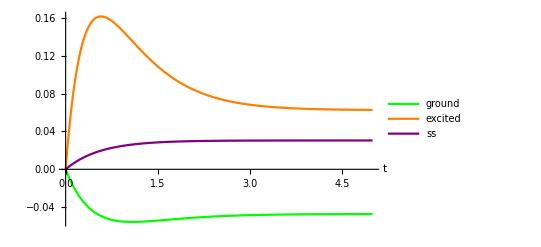

```mathematica
Ω=1;γw=1;γm=0.2; 
varGroundEvol = ListPlot[Table[{t,-(4 ⅇ^(-2 t (4 γm+γw)) γm^2 γw^2)/(4 γm+γw)^4-(2 γm γw (16 γm^2-2 γm γw+γw^2))/(4 γm+γw)^4-(2 ⅇ^(-t (4 γm+γw)) γm γw (-16 γm^2+32 t γm^2 γw-γw^2+8 t γm γw^2))/(4 γm+γw)^4},{t,0,5,0.01}],Joined->True, PlotStyle->Directive[Solid,Green],AxesLabel->{Style["t",20,Black]}];

varExcitedEvol = ListPlot[Table[{t,(γw (32 γm^3+20 γm^2 γw-2 γm γw^2))/(4 γm+γw)^4+(ⅇ^(-2 t (4 γm+γw)) γw (-4 γm^2 γw-4 γm γw^2-γw^3))/(4 γm+γw)^4+(ⅇ^(-t (4 γm+γw)) γw (-32 γm^3-16 γm^2 γw+64 t γm^3 γw+6 γm γw^2+48 t γm^2 γw^2+γw^3+8 t γm γw^3))/(4 γm+γw)^4},{t,0,5,0.01}],Joined->True, PlotStyle->Directive[Solid,Orange],AxesLabel->{Style["t",20,Black]}];


varSsEvol = ListPlot[Table[{t,-(8 (-1+ⅇ^(-t (4 γm+γw))) γm^2 γw^2)/(4 γm+γw)^4},{t,0,5,0.01}],Joined->True, PlotStyle->Directive[Solid,Purple],AxesLabel->{Style["t",20,Black]}];
Legended[Show[varGroundEvol ,varExcitedEvol,varSsEvol ,PlotRange->All],LineLegend[{Directive[Green,Solid],Directive[Orange,Solid],Directive[Solid,Purple]},{"ground","excited","ss"}]]
```